## NLL Angularities with Shape Function

### Baseline Values

```mathematica
αsCR baseline=(*0.117998;*)0.1185;
NF baseline = 5;
Ω0 baseline = 0.21;  (*in GeV this number needs to be checked *)
Ω0 tiny = 0.00001; (* used for quasi-parton cross check *)

Ξ0 baseline = 0.34;  (*in GeV this number needs to be checked *)
Ξ0 tiny = 0.00001; (* used for quasi-parton cross check *)

Ω0 baseline noC = 0.40; (*in GeV this number needs to be checked *)
Ξ0 baseline noC = 0.64;
```

### Physical Constants

```mathematica
mZ=91.19;
β0=11/(4π)-5/(6π);
β1=153/(24 π^2)-75/(24 π^2)-20/(24 π^2);
K=(67/6-π^2/2)-25/9;
CF = 4/3;
CA = 3;
Bq =-3/4;
Bg[NF_]:=-(33-2NF)/36;
aNGL = 0.85*CA;
bNGL = 0.86*CA;
cNGL = 1.33;
```

### Angularites: Perturbative Cumulative Distribution

```mathematica
AngularitiesMasterCumulative[τ1_, Cfactor_, Bfactor_,αsCR_,  R_, Q_, use2loop_, useNGL_, β_]:= Block[{L,t, NGL, αs,λ, r,T,Talt,dr,ANS, kt},

kt = Q* R /2.0; (* factor of two because jet energy is half of collision energy in e+e-*)
L=Log[1/τ1];
αs=(1/αsCR+23/(6π)Log[kt/mZ]+116/(92π)Log[1+23/(6π)αsCR Log[kt/mZ]])^-1;
λ=αs*β0*L;
r=L/(2π β0 λ(β-1))((1-2λ)Log[1-2λ]-(β-2λ)Log[1-(2λ)/β])+use2loop*1/(β-1)(K/(4 π^2 β0^2)(β Log[1-(2λ)/β]-Log[1-2λ])+β1/(2π β0^3)(Log[1-2λ]^2/2-β/2 Log[1-(2λ)/β]^2+Log[1-2λ]-β Log[1-(2λ)/β]));
T=-1/(π β0)Log[1-2λ];
t = T/4;
Talt=-1/(π β0)Log[1-(2λ)/β];
dr=1/(β-1)(T-Talt);

NGL = Exp[-useNGL* Cfactor *CA π^2/3((1 + (aNGL*t)^2)/(1 + (bNGL*t)^cNGL) )t^2];

ANS =NGL* ⅇ^(-EulerGamma Cfactor dr)/Gamma[1+Cfactor dr] ⅇ^(-Cfactor(r+Bfactor  Talt));
If[1-2λ>0 && 1-(2λ)/β>0 && αs>0,Evaluate[ANS],0.0]
]
```

### Defining Benchmarks

```mathematica
(* Baseline*)
AngularitiesCumulative[τ1_,"baseline","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 1,1, β]
AngularitiesCumulative[τ1_,"baseline","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R, Q, 1,1,β]

(* noCas and altF, doesn't change perturbative *)
AngularitiesCumulative[τ1_,"noCas","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 1,1, β]
AngularitiesCumulative[τ1_,"noCas","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R, Q, 1,1,β]

AngularitiesCumulative[τ1_,"altF","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 1,1, β]
AngularitiesCumulative[τ1_,"altF","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R, Q, 1,1,β]

(* No g -> qq, only gluon has to change *)
AngularitiesCumulative[τ1_,"nogqq","quark", R_, Q_, β_]:=AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 1,1,β]
AngularitiesCumulative[τ1_,"nogqq","gluon", R_, Q_ ,β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[0], αsCR baseline, R, Q, 1,1,β]

(* No 2loop effects *)
AngularitiesCumulative[τ1_,"no2loop","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 0, 1,β]
AngularitiesCumulative[τ1_,"no2loop","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R, Q, 0,1,β]

(* No NGL effects *)
AngularitiesCumulative[τ1_,"noNGL","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 1, 0,β]
AngularitiesCumulative[τ1_,"noNGL","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R, Q, 1,0,β]

(* αs sweep *)
AngularitiesCumulative[τ1_,"alphasx08","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 0.8*αsCR baseline, R, Q,1,1, β]
AngularitiesCumulative[τ1_,"alphasx09","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 0.9*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx10","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 1*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx11","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 1.1*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx12","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 1.2*αsCR baseline,R, Q,1,1, β]

AngularitiesCumulative[τ1_,"alphasx08","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 0.8*αsCR baseline, R, Q, 1,1,β]
AngularitiesCumulative[τ1_,"alphasx09","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 0.9*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx10","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 1*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx11","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 1.1*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx12","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 1.2*αsCR baseline,R, Q,1, 1,β]
```

### Angularities: Perturbative Differential Distribution and Lists/Interpolations

```mathematica
(* defining generic parton-level*)
Clear[AngularitiesDifferentialList, AngularitiesDifferentialInterpolation]

(* Have to start with zero for this to work*)
τ1max = 1;
τ1nbins = 500;
τ1diff = τ1max/τ1nbins;
τ1order = 1;

AngularitiesDifferentialList[ "parton",para_, sample_, R_,Q_,β_]:=  AngularitiesDifferentialList[ "parton", para, sample, R,Q, β] =Block[{cumlist, cumlistL, cumlistR, centers, derivs},
cumlist = Join[{{0,0}},Table[{τ1,Max[Re[AngularitiesCumulative[τ1 , para, sample, R,Q,β]],0.0]}, {τ1,τ1diff,τ1max-τ1diff,τ1diff}],{ {τ1max,1}}]; 
cumlistL = Rest[cumlist];
cumlistR = Most[cumlist];

centers = (cumlistL[[All,1]] + cumlistR[[All,1]])/2;
derivs = (cumlistL[[All,2]] - cumlistR[[All,2]])/τ1diff;
derivs =  Max[#,0]&/@ derivs;
derivs = derivs/Total[derivs]/τ1diff;
 Transpose[{centers,derivs}] 
]

AngularitiesDifferentialInterpolation[type_, para_, sample_, R_,Q_, β_]:= AngularitiesDifferentialInterpolation[type, para, sample, R,Q, β] = Interpolation[AngularitiesDifferentialList[type, para, sample, R,Q, β], InterpolationOrder->τ1order]
```

### Non-perturbative Corrections

```mathematica
GenericShapeFunction[δ_, δ0_]:=(ⅇ^(-(π δ^2)/(4 δ0^2)) π δ)/(2 δ0^2)
GenericShapeFunctionAlt[δ_, δ0_]:= (4δ)/δ0^2 ⅇ^(-(2δ)/δ0)  
(*GenericShapeCumulative[δ_,δ0_]:=(δ0-ⅇ^(-(2 δ)/δ0) (2 δ+δ0))/δ0 (*(δ0-ⅇ^(-(2 δ)/δ0) (2 δ+δ0))/δ0; *) (*  1-ⅇ^(-(π δ^2)/(4 δ0^2))*) (*If[δ<2 δ0, -(3 (δ^3/3-δ^2 δ0))/(4 δ0^3), 1]*) *)

(* Dividing by 2 since Q is collision energy, but power correction is related to jet energy *)
AngularitiesNonPerturbativeShift[Ω0_,Ξ0_, R_, Q_, β_]:=Ω0/(R* Q/2.0) (1 - (Ξ0/(R*Q/2.0))^(β-1))/(β - 1);

color of["quark"]:= CF;
color of["gluon"]:= CA;

(*ShapeCumulative[δ_,"hadron",para_, sample_,  R_,Q_,β_]:= GenericShapeCumulative[δ, AngularitiesNonPerturbativeShift[color of[sample]* Ω0 baseline,color of[sample]* Ξ0 baseline,R,Q, β]]
ShapeCumulative[δ_,"hadron","noCas", sample_,  R_,Q_,β_]:= GenericShapeCumulative[δ, AngularitiesNonPerturbativeShift[ Ω0 baseline noC,Ξ0 baseline noC,R,Q, β]]*)
(*ShapeCumulative[δ_,"quasi-parton",para_, sample_,R_,Q_ ,β_]:= GenericShapeCumulative[δ,AngularitiesNonPerturbativeShift[Ω0 tiny,Ξ0 tiny ,R,Q, β]]*)

ShapeFunction[δ_,"hadron",para_, sample_,  R_,Q_,β_]:= GenericShapeFunction[δ, AngularitiesNonPerturbativeShift[color of[sample]* Ω0 baseline,color of[sample]* Ξ0 baseline,R,Q, β]]
ShapeFunction[δ_,"hadron","noCas", sample_,  R_,Q_,β_]:= GenericShapeFunction[δ, AngularitiesNonPerturbativeShift[ Ω0 baseline noC,Ξ0 baseline noC,R,Q, β]]
ShapeFunction[δ_,"hadron","altF", sample_,  R_,Q_,β_]:= GenericShapeFunctionAlt[δ, AngularitiesNonPerturbativeShift[color of[sample]* Ω0 baseline,color of[sample]* Ξ0 baseline,R,Q, β]]

(*Clear[ShapeDifferentialList]

ShapeDifferentialList[type_,para_, sample_,R_,Q_, β_]:=  ShapeDifferentialList[type, para, sample, R,Q,β] =Block[{cumlist, cumlistL, cumlistR, centers, derivs},
cumlist = Join[{{0,0}},Table[{τ1,Max[Re[ShapeCumulative[τ1 ,type, para, sample,R,Q, β]],0.0]}, {τ1,τ1diff,τ1max-τ1diff,τ1diff}],{{τ1max ,1}}]; 
cumlistL = Rest[cumlist];
cumlistR = Most[cumlist];

centers = (cumlistL[[All,1]] + cumlistR[[All,1]])/2;
derivs = (cumlistL[[All,2]] - cumlistR[[All,2]])/τ1diff;
(* next two steps probably aren't needed, but putting in anyways *)
derivs =  Max[#,0.0]&/@ derivs;
derivs = derivs/Total[derivs]/τ1diff;
 Transpose[{centers,derivs}] 
]*)

Clear[ShapeFunctionMatrix]

ShapeFunctionMatrix[type_,para_, sample_, R_,Q_,β_]:= ShapeFunctionMatrix[ type, para, sample, R,Q, β]= 
Block[{i,j, shapefunc},
shapefunc = ShapeFunction[#,type,para, sample,  R,Q,β]&;
(* Note the Jacobian factor! *)
Table[If[τf> τp, shapefunc[(τf - τp)/(1-τf/τ1max)]*(τ1max  (τ1max-τp))/(τf-τ1max)^2 τ1diff, 0], {τf,τ1diff/2,τ1max-τ1diff/2,τ1diff},{τp,τ1diff/2,τ1max-τ1diff/2,τ1diff}]
];

(* This technique only works if parton and shape have the same length, parton and shape have zero entries at 0, and equally spaced yada yada *)
AngularitiesDifferentialList[ type_,para_, sample_, R_,Q_,β_]:=  AngularitiesDifferentialList[ type, para, sample, R,Q, β]  = Block[{parton,partonvalues, shapematrix, coords, hadron,paraalt},
parton = AngularitiesDifferentialList[ "parton", para, sample,R,Q,  β];
partonvalues =  parton[[All,2]];
coords = parton[[All,1]];
paraalt = If[para== "noCas" || para == "altF", para, "baseline"];
shapematrix= ShapeFunctionMatrix[type, paraalt, sample,R,Q,  β];
hadron =Transpose[ shapematrix.Transpose[{partonvalues}]][[1]];
Transpose[{coords,hadron}]

(*parton = AngularitiesDifferentialList[ "parton", para, sample,R,Q,  β];
shape = ShapeDifferentialList[type, para, sample,R,Q,  β];

(* This technique only works if parton and shape have the same length, parton and shape have zero entries at 0, and equally spaced yada yada *)
coords = parton[[All,1]];
partonvalues =  parton[[All,2]];
shapevalues =  shape[[All,2]];

length= Length[coords];

total = Table[0, {k,1, Length[coords]}];

For[i=1, i <= length, i++,
For[j=1, j <= length, j++,
(*coord =Round[ i+j*(Max[(length-(i+j-1))/length, 0])-1];*)
coord =Round[ (i+j)/(length + j)*length];
coord =Max[ Min[coord, length],1];
addend =  partonvalues[[i]]*shapevalues[[j]]*τ1diff;
total[[coord]] +=addend;
(*shapevalues = Join[{0},Most[shapevalues]]*)
(*shapevalues = ArrayPad[Drop[shapevalues,-1-0], {1,0}]*)
];
];*)


(*For[i=1, i < Length[coords], i++,
total += partonvalues[[i]]*shapevalues*τ1diff;
(*shapevalues = Join[{0},Most[shapevalues]]*)
shapevalues = ArrayPad[Drop[shapevalues,-1-0], {1,0}]
];*)

(*For[i=1, i < Length[coords], i++,
total += shapevalues[[i]]*partonvalues*τ1diff;
partonvalues = Join[{0},Most[partonvalues]]
(*partonvalues = ArrayPad[Drop[partonvalues,-1-i], {1,i}]*)
];*)

(*Transpose[{coords,total}]*)
]
```

## Outputting Distributions

```mathematica
SetDirectory[NotebookDirectory[]]

R baseline  = 0.6;
R values = {0.2,0.4,0.6,0.8,1.0}
R name[0.2]= "R02";
R name[0.4]= "R04";
R name[0.6]= "R06";
R name[0.8]= "R08";
R name[1.0]= "R10";

Q baseline = 200.0 ;
Q values = {50,100,200,400,800}
Q name[50]= "50";
Q name[100]= "100";
Q name[200]= "200";
Q name[400]= "400";
Q name[800]= "800";

β baseline = 0.5 ;
βone = 1.0001;
β values = {0.5,βone,2.0};
β name[0.5] = "beta05";
β name[βone] = "beta10";
β name[2.0] = "beta20";

MakeMinMax[{xmin_,value_}]:= {N[xmin- τ1diff/2],N[xmin+ τ1diff/2],N[Round[value*100000]/100000]}

OutputFilesForSetting[para_, R_, Q_, β_]:= Module[{one,two,three,four},
one =  MakeMinMax/@ AngularitiesDifferentialList["parton",para,"quark", R,Q,β];
Export["parton/uu-"<>Q name[Q]<>"-"<>If[para == "baseline", "", para<>"-"]<> β name[β] <> "-" <>R name[R]<>".txt",one, "Table"];
two = MakeMinMax/@ AngularitiesDifferentialList["parton",para,"gluon", R,Q,β];
Export["parton/gg-"<>Q name[Q]<>"-"<>If[para == "baseline", "", para<>"-"]<> β name[β] <> "-" <>R name[R]<>".txt",two, "Table"];
three = MakeMinMax/@ AngularitiesDifferentialList["hadron",para,"quark", R,Q,β];
Export["hadron/uu-"<>Q name[Q]<>"-"<>If[para == "baseline", "", para<>"-"]<> β name[β] <> "-" <>R name[R]<>".txt",three, "Table"];
four = MakeMinMax/@ AngularitiesDifferentialList["hadron",para,"gluon", R,Q,β];
Export["hadron/gg-"<>Q name[Q]<>"-"<>If[para == "baseline", "", para<>"-"]<> β name[β] <> "-" <>R name[R]<>".txt",four, "Table"];
]

OutputFilesForSetting[para_]:= Module[{},
Outer[OutputFilesForSetting[para, #1,#2,#3]&, R values, Q values, β values]
]
```

/Users/jthaler/outside/lh2015-qg/AnalyticResum

{0.2,0.4,0.6,0.8,1.}

{50,100,200,400,800}

```mathematica
OutputFilesForSetting["baseline"]
```

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

```mathematica
OutputFilesForSetting["nogqq"]
OutputFilesForSetting["no2loop"]
OutputFilesForSetting["noNGL"]
OutputFilesForSetting["alphasx08"]
OutputFilesForSetting["alphasx09"]
OutputFilesForSetting["alphasx10"]
OutputFilesForSetting["alphasx11"]
OutputFilesForSetting["alphasx12"]
```

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

«5 more identical outputs»

```mathematica
OutputFilesForSetting["noCas"]
OutputFilesForSetting["altF"]
```

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

## Binning and Classifier Separation

```mathematica
QGClassifierSeparation[type_, para_, R_,Q_,β_]:= Block[{quarklist, gluonlist,answer, integrand},
quarklist = AngularitiesDifferentialList[type, para, "quark",R,Q, β][[All,2]];
gluonlist = AngularitiesDifferentialList[type, para, "gluon",R,Q, β][[All,2]];
integrand = (quarklist - gluonlist + ϵ)^2 / (2(quarklist+gluonlist + ϵ)) /. ϵ -> 0;
answer = Total[integrand]*τ1diff
]
```

## Checking Partonic Results

2.

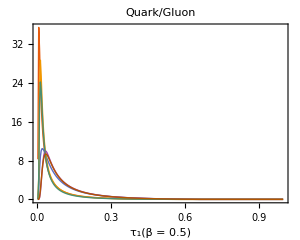

```mathematica
β baseline = 2.0
Plot[{
AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["hadron", "altF","quark",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["hadron", "altF","gluon",R baseline, Q baseline,β baseline][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
```

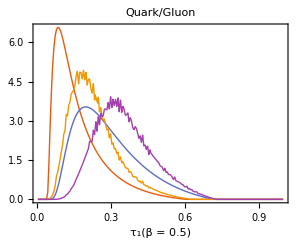

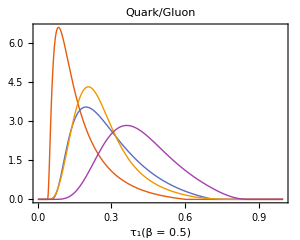

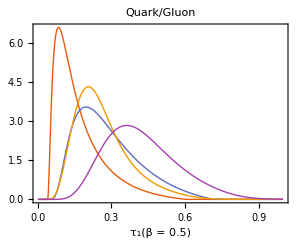

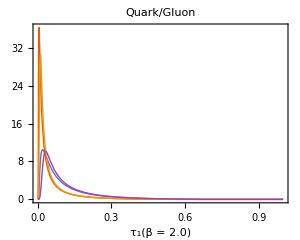

```mathematica
Plot[{
AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, Q baseline,2.0][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline, Q baseline,2.0][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline, Q baseline,2.0][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline, Q baseline,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 2.0)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
```

### Basic Partonic Distribution

0.263832

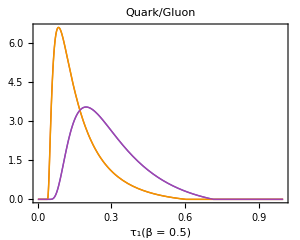
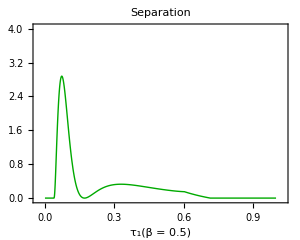

```mathematica
QGClassifierSeparation["parton", "baseline",R baseline, Q baseline, β baseline]

{
Plot[{
AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["quasi-parton", "baseline","quark",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["quasi-parton", "baseline","gluon",R baseline, Q baseline,β baseline][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
,
Plot[{
(AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, Q baseline,β baseline][τ1] - AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline, Q baseline,β baseline][τ1])^2/(2(AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, Q baseline,β baseline][τ1] + AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline, Q baseline,β baseline][τ1] + 0.000000000001))},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Separation",
PlotStyle->Directive[Thick,Darker[Green]], Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8, PlotRange-> {{-0.03,1.03}, {-0.03,4.03}}]
}
```

```mathematica
{QGClassifierSeparation["parton", "baseline",R baseline, Q baseline, 0.5],QGClassifierSeparation["parton", "baseline",R baseline, Q baseline, βone],QGClassifierSeparation["parton", "baseline",R baseline, Q baseline, 2.0]}
{QGClassifierSeparation["parton", "nogqq",R baseline, Q baseline, 0.5],QGClassifierSeparation["parton", "nogqq",R baseline, Q baseline, βone],QGClassifierSeparation["parton", "nogqq",R baseline, Q baseline, 2.0]}
{QGClassifierSeparation["parton", "no2loop",R baseline, Q baseline, 0.5],QGClassifierSeparation["parton", "no2loop",R baseline, Q baseline, βone],QGClassifierSeparation["parton", "no2loop",R baseline, Q baseline, 2.0]}
```

{0.263832,0.206307,0.170867}

{0.20133,0.167274,0.147908}

{0.275862,0.21367,0.174916}

```mathematica
(* Q sweep *)
QGClassifierSeparation["parton", "baseline",R baseline,#, β baseline]&/@ Q values

(* R sweep *)
QGClassifierSeparation["parton", "baseline",#,Q baseline, β baseline]&/@ R values
(* αs sweep *)
{QGClassifierSeparation["parton", "alphasx08", R baseline,Q baseline, β baseline],
QGClassifierSeparation["parton", "alphasx09",R baseline,Q baseline, β baseline],
QGClassifierSeparation["parton", "alphasx10",R baseline,Q baseline, β baseline],
QGClassifierSeparation["parton", "alphasx11",R baseline,Q baseline, β baseline],
QGClassifierSeparation["parton", "alphasx12",R baseline,Q baseline, β baseline]}
```

{0.284118,0.273333,0.263832,0.255419,0.247932}

{0.279472,0.269246,0.263832,0.260218,0.257536}

{0.245215,0.254939,0.263832,0.271972,0.279433}

### Basic Hadronic Distributions

{0.206307,0.279916}

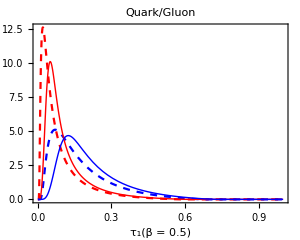
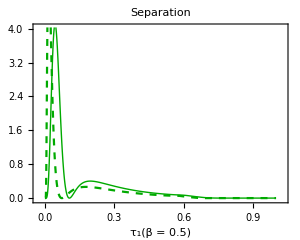

```mathematica
β test = 1.0001;
{QGClassifierSeparation["parton", "baseline", R baseline,Q baseline,β test],QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, β test]}
{
Plot[{AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline,Q baseline,β test][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline,Q baseline,β test][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline,Q baseline,β test][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline,Q baseline,β test][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->{Directive[Dashed, Red],Directive[Dashed, Blue],Directive[Thick, Red],Directive[Thick, Blue]}, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
,
Plot[{(AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline,Q baseline,β test][τ1] - AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline,Q baseline,β test][τ1])^2/(2(AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline,Q baseline,β test][τ1] + AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline,Q baseline,β test][τ1] + 0.000000000001)),
(AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline,Q baseline,β test][τ1] - AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline,Q baseline,β test][τ1])^2/(2(AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline,Q baseline,β test][τ1] + AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline,Q baseline,β test][τ1] + 0.000000000001))},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Separation",
PlotStyle->{Directive[Dashed,Darker[Green]],Directive[Thick,Darker[Green]]}, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8, PlotRange-> {{-0.03,1.03}, {-0.03,4.03}}]
}
```

{0.263832,0.303124}

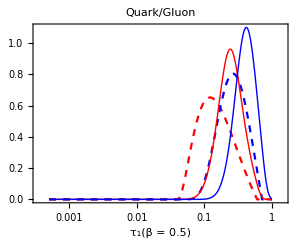

```mathematica
{QGClassifierSeparation["parton", "baseline",R baseline,Q baseline, β baseline],QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, β baseline]}

LogLinearPlot[{AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline,Q baseline,β baseline][τ1]*τ1,
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline,Q baseline,β baseline][τ1]*τ1,
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline,Q baseline,β baseline][τ1]*τ1,
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline,Q baseline,β baseline][τ1]*τ1
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->{Directive[Dashed, Red],Directive[Dashed, Blue],Directive[Thick, Red],Directive[Thick, Blue]}, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
```

```mathematica
{QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, 0.5],QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, βone],QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, 2.0]}
{QGClassifierSeparation["hadron", "nogqq", R baseline,Q baseline,0.5],QGClassifierSeparation["hadron", "nogqq",R baseline,Q baseline, βone],QGClassifierSeparation["hadron", "nogqq", R baseline,Q baseline,2.0]}
{QGClassifierSeparation["hadron", "no2loop",R baseline,Q baseline, 0.5],QGClassifierSeparation["hadron", "no2loop",R baseline,Q baseline, βone],QGClassifierSeparation["hadron", "no2loop",R baseline,Q baseline, 2.0]}
```

{0.303124,0.279916,0.223215}

{0.240916,0.241957,0.202635}

{0.312158,0.28943,0.231084}

```mathematica
(* Q sweep *)
QGClassifierSeparation["hadron", "baseline",R baseline,#, β baseline]&/@ Q values

(* R sweep *)
QGClassifierSeparation["hadron", "baseline",#,Q baseline, β baseline]&/@ R values
(* αs sweep *)
{QGClassifierSeparation["hadron", "alphasx08", R baseline,Q baseline, β baseline],
QGClassifierSeparation["hadron", "alphasx09",R baseline,Q baseline, β baseline],
QGClassifierSeparation["hadron", "alphasx10",R baseline,Q baseline, β baseline],
QGClassifierSeparation["hadron", "alphasx11",R baseline,Q baseline, β baseline],
QGClassifierSeparation["hadron", "alphasx12",R baseline,Q baseline, β baseline]}
```

{0.267144,0.29524,0.303124,0.300967,0.293589}

{0.282205,0.300218,0.303124,0.303093,0.30218}

{0.280242,0.292471,0.303124,0.312479,0.320747}

## Trying to get NP shift right

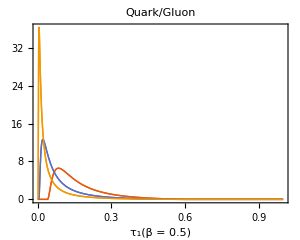

```mathematica
Plot[{
AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
Plot[{
AngularitiesDifferentialInterpolation["parton", "noCas","quark",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["parton", "noCas","quark",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["parton", "noCas","quark",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
(*Plot[{
AngularitiesDifferentialInterpolation["hadron", "no2loop","gluon",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "no2loop","gluon",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "no2loop","gluon",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
Plot[{
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
Plot[{
AngularitiesDifferentialInterpolation["hadron", "noNGL","gluon",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "noNGL","gluon",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "noNGL","gluon",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];*)

Show[%,%%]


(*Plot[{
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 50,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 50,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 50,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]*)
```

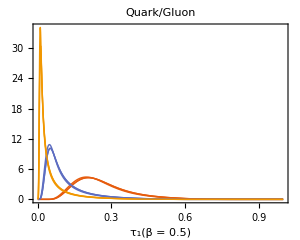

```mathematica
Plot[{
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
Plot[{
AngularitiesDifferentialInterpolation["hadron", "no2loop","quark",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "no2loop","quark",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "no2loop","quark",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
Plot[{
AngularitiesDifferentialInterpolation["hadron", "nogqq","quark",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","quark",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","quark",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];

Show[%,%%,%%%]
```